# Calculo de Chi.b2 con los datos de Maltoni y LAL

## Descripción de los Braching ratios de las ecuaciones en el LAL

#### Braching ratios J/ψ

```mathematica
(* Falta masac^2*)
(*Ecuación 19, Subscript[O, 1]((.b3S)_1), Subscript[O, 8]((.b3S)_1), Subscript[O, 8]((.b9S)_0) y Subscript[O, 8]((.b3P)_0)*)
B1ψ[x_,y_,z_,w_]=7.54*10^(-4)x+0.195y+0.342*z+1.06*w;
B2ψ[x_,y_,z_,w_]=4.84*10^(-4)x+0.193y+0.338*z+1.05*w;
B3ψ[x_,y_,z_,w_]=8.13*10^(-4)x+0.325y+0.57*z+1.76*w;
B4ψ[x_,y_,z_,w_]=7.31*10^(-4)x+0.277y+0.496*z+1.61*w;
```

#### Operadores η

```mathematica
L11 = 0.125*10^(-2)*1/3;
L12 = 0.338*1/3;
L13 = 0.193;
L14 = -0.0464*3;

L21 = 0.209*10^(-2)*1/3;
L22 = 0.569*1/3;
L23 = 0.325;
L24 = -0.0780*3;

L31 = 0.178*10^(-2)*1/3;
L32 = 0.411*1/3;
L33 = 0.240;
L34 = -0.0780*3;
```

#### Braching ratios η

```mathematica
(*Ecuación 20, Subscript[O, 1]((.b3S)_1), Subscript[O, 8]((.b3S)_1), Subscript[O, 8]((.b9S)_0) y Subscript[O, 8]((.b3P)_0)*)
B1η[x_,y_,z_,w_]=8.33*10^(-4)x+0.114y+0.195*z-0.1404w;
B2η[x_,y_,z_,w_]=L11*10^(-4)x+L12*y+L13*z-L14*w;
B3η[x_,y_,z_,w_]=6.967*10^(-4)x+0.19y+0.325*z-0.234w;
B4η[x_,y_,z_,w_]=5.096*10^(-4)x+0.1654y+0.2777*z-0.1393w;
```

#### Se definen los Braching ratios de χc

```mathematica
Subscript[B1, χc0][x_,y_]=-0.0148x+0.195y ;        (*Ecuación 21,  Subscript[O, 1] y Subscript[O, 8]*)
Subscript[B2, χc0][x_,y_]=-0.0147x+0.193y ;        (*Ecuación 21,  Subscript[O, 1] y Subscript[O, 8]*)
Subscript[B3, χc0][x_,y_]=-0.0247x+0.325y ;        (*Ecuación 21,  Subscript[O, 1] y Subscript[O, 8]*)
Subscript[B4, χc0][x_,y_]=-0.0147x+0.277y ;        (*Ecuación 21,  Subscript[O, 1] y Subscript[O, 8]*)
(*-------------------------------------------------------------*)
Subscript[B1, χc1][x_,y_]=-0.0234x+0.585y  ;        (*Ecuación 22,  Subscript[O, 1] y Subscript[O, 8]*)
Subscript[B2, χc1][x_,y_]=-0.0256x+0.579y  ;        (*Ecuación 22,  Subscript[O, 1] y Subscript[O, 8]*)
Subscript[B3, χc1][x_,y_]=-0.04311x+0.975y  ;        (*Ecuación 22,  Subscript[O, 1] y Subscript[O, 8]*)
Subscript[B4, χc1][x_,y_]=-0.04551x+0.8332y  ;        (*Ecuación 22,  Subscript[O, 1] y Subscript[O, 8]*)
(*-------------------------------------------------------------*)
Subscript[B1, χc2][x_,y_]=-0.0600x+0.975y   ;         (*Ecuación 23,  Subscript[O, 1] y Subscript[O, 8]*)
Subscript[B2, χc2][x_,y_]=-0.0595x+0.965y   ;         (*Ecuación 23,  Subscript[O, 1] y Subscript[O, 8]*)
Subscript[B3, χc2][x_,y_]=-0.100x+1.625y   ;         (*Ecuación 23,  Subscript[O, 1] y Subscript[O, 8]*)
Subscript[B4, χc2][x_,y_]=-0.05945x+1.388y   ;         (*Ecuación 23,  Subscript[O, 1] y Subscript[O, 8]*)
```

#### Función de error

```mathematica
error[x_,y_,z_]=Sqrt[x^2+y^2+z^2];
```

#### Chi.b2 calculado de la división teórica de las funciones expresadas anteriormente y los datos experimental con sus tres errores para η y ψ

```mathematica
(*Ecuación 8 del LAL resultado experimental*)
Subscript[χ1B, η/ψ][x_,y_,z_,w_]=((B1η[x,y,z,w]/B1ψ[x,y,z,w]-0.691)/error[0.09,0.024,0.103])^2;
(*Data group*)
Subscript[χ1B, ψ][x_,y_,z_,w_]=((B1ψ[x,y,z,w]-7.8*10^(-3))/0.4*10^(-3))^2;
(*Promediar para analizar como es el comportamiento del conjunto*)
Subscript[χ1B, ψ-η/ψ][x_,y_,z_,w_]=(Subscript[χ1B, ψ][x,y,z,w]+Subscript[χ1B, η/ψ][x,y,z,w])/2;
(*---------------------------------------------------------------------------------------------*)
(*Ecuación 8 del LAL resultado experimental*)
Subscript[χ2B, η/ψ][x_,y_,z_,w_]=((B2η[x,y,z,w]/B2ψ[x,y,z,w]-0.691)/error[0.09,0.024,0.103])^2;
(*Data group*)
Subscript[χ2B, ψ][x_,y_,z_,w_]=((B2ψ[x,y,z,w]-7.8*10^(-3))/0.4*10^(-3))^2;
(*Promediar para analizar como es el comportamiento del conjunto*)
Subscript[χ2B, ψ-η/ψ][x_,y_,z_,w_]=(Subscript[χ2B, ψ][x,y,z,w]+Subscript[χ2B, η/ψ][x,y,z,w])/2;
(*---------------------------------------------------------------------------------------------*)
(*Ecuación 8 del LAL resultado experimental*)
Subscript[χ3B, η/ψ][x_,y_,z_,w_]=((B3η[x,y,z,w]/B3ψ[x,y,z,w]-0.691)/error[0.09,0.024,0.103])^2;
(*Data group*)
Subscript[χ3B, ψ][x_,y_,z_,w_]=((B3ψ[x,y,z,w]-7.8*10^(-3))/0.4*10^(-3))^2;
(*Promediar para analizar como es el comportamiento del conjunto*)
Subscript[χ3B, ψ-η/ψ][x_,y_,z_,w_]=(Subscript[χ3B, ψ][x,y,z,w]+Subscript[χ3B, η/ψ][x,y,z,w])/2;
(*---------------------------------------------------------------------------------------------*)
(*Ecuación 8 del LAL resultado experimental*)
Subscript[χ4B, η/ψ][x_,y_,z_,w_]=((B4η[x,y,z,w]/B4ψ[x,y,z,w]-0.691)/error[0.09,0.024,0.103])^2;
(*Data group*)
Subscript[χ4B, ψ][x_,y_,z_,w_]=((B4ψ[x,y,z,w]-7.8*10^(-3))/0.4*10^(-3))^2;
(*Promediar para analizar como es el comportamiento del conjunto*)
Subscript[χ4B, ψ-η/ψ][x_,y_,z_,w_]=(Subscript[χ4B, ψ][x,y,z,w]+Subscript[χ4B, η/ψ][x,y,z,w])/2;
```

#### Chi.b2 calculado de la división teórica de las funciones expresadas anteriormente y los datos experimental con sus tres errores para χc

```mathematica
(*Ecuación 9 del LAL resultado experimental*)
Subscript[χ2B1, χc0][x_,y_]=((Subscript[B1, χc0][x,y]-2.74*10^(-3))/error[0.47*10^(-3),0.23*10^(-3),0.94*10^(-3)])^2;
(*Ecuación 10 del LAL resultado experimental*)
Subscript[χ2B1, χc1][x_,y_]=((Subscript[B1, χc1][x,y]-2.49*10^(-3))/error[0.59*10^(-3),0.23*10^(-3),0.89*10^(-3)])^2;
(*Ecuación 11 del LAL resultado experimental*)
Subscript[χ2B1, χc2][x_,y_]=((Subscript[B1, χc2][x,y]-0.89*10^(-3))/error[0.20*10^(-3),0.07*10^(-3),0.36*10^(-3)])^2;
(*Promedio  ?*)
Subscript[χ2B1, χc][x_,y_]=(Subscript[χ2B1, χc0][x,y]+Subscript[χ2B1, χc1][x,y]+Subscript[χ2B1, χc2][x,y])/3;
(*-------------------------------------------------------------------------------------------------------*)
(*Ecuación 9 del LAL resultado experimental*)
Subscript[χ2B2, χc0][x_,y_]=((Subscript[B2, χc0][x,y]-2.74*10^(-3))/error[0.47*10^(-3),0.23*10^(-3),0.94*10^(-3)])^2;
(*Ecuación 10 del LAL resultado experimental*)
Subscript[χ2B2, χc1][x_,y_]=((Subscript[B2, χc1][x,y]-2.49*10^(-3))/error[0.59*10^(-3),0.23*10^(-3),0.89*10^(-3)])^2;
(*Ecuación 11 del LAL resultado experimental*)
Subscript[χ2B2, χc2][x_,y_]=((Subscript[B2, χc2][x,y]-0.89*10^(-3))/error[0.20*10^(-3),0.07*10^(-3),0.36*10^(-3)])^2;
(*Promedio  ?*)
Subscript[χ2B2, χc][x_,y_]=(Subscript[χ2B2, χc0][x,y]+Subscript[χ2B2, χc1][x,y]+Subscript[χ2B2, χc2][x,y])/3;
(*-------------------------------------------------------------------------------------------------------*)
(*Ecuación 9 del LAL resultado experimental*)
Subscript[χ2B3, χc0][x_,y_]=((Subscript[B3, χc0][x,y]-2.74*10^(-3))/error[0.47*10^(-3),0.23*10^(-3),0.94*10^(-3)])^2;
(*Ecuación 10 del LAL resultado experimental*)
Subscript[χ2B3, χc1][x_,y_]=((Subscript[B3, χc1][x,y]-2.49*10^(-3))/error[0.59*10^(-3),0.23*10^(-3),0.89*10^(-3)])^2;
(*Ecuación 11 del LAL resultado experimental*)
Subscript[χ2B3, χc2][x_,y_]=((Subscript[B3, χc2][x,y]-0.89*10^(-3))/error[0.20*10^(-3),0.07*10^(-3),0.36*10^(-3)])^2;
(*Promedio  ?*)
Subscript[χ2B3, χc][x_,y_]=(Subscript[χ2B3, χc0][x,y]+Subscript[χ2B3, χc1][x,y]+Subscript[χ2B3, χc2][x,y])/3;
(*-------------------------------------------------------------------------------------------------------*)
(*Ecuación 9 del LAL resultado experimental*)
Subscript[χ2B4, χc0][x_,y_]=((Subscript[B4, χc0][x,y]-2.74*10^(-3))/error[0.47*10^(-3),0.23*10^(-3),0.94*10^(-3)])^2;
(*Ecuación 10 del LAL resultado experimental*)
Subscript[χ2B4, χc1][x_,y_]=((Subscript[B4, χc1][x,y]-2.49*10^(-3))/error[0.59*10^(-3),0.23*10^(-3),0.89*10^(-3)])^2;
(*Ecuación 11 del LAL resultado experimental*)
Subscript[χ2B4, χc2][x_,y_]=((Subscript[B4, χc2][x,y]-0.89*10^(-3))/error[0.20*10^(-3),0.07*10^(-3),0.36*10^(-3)])^2;
(*Promedio  ?*)
Subscript[χ2B4, χc][x_,y_]=(Subscript[χ2B4, χc0][x,y]+Subscript[χ2B4, χc1][x,y]+Subscript[χ2B4, χc2][x,y])/3;
```

#### Chi.b2 calculado de la división teórica de las funciones expresadas anteriormente y los datos experimental con sus tres errores para χc/χc0

```mathematica
(*Ecuación 12 del LAL resultado experimental*)
Subscript[χ2B1, χc1/χc0][x_,y_]=(((Subscript[B1, χc1][x,y]/Subscript[B1, χc0][x,y])-0.91)/error[0.20,0.02,0.15])^2;
(*Ecuación 13 del LAL resultado experimental*)
Subscript[χ2B1, χc2/χc0][x_,y_]=(((Subscript[B1, χc2][x,y]/Subscript[B1, χc0][x,y])-0.34)/error[0.06,0.01,0.05])^2;
(*Promedio*)
Subscript[χ2B1, χc/χc0][x_,y_]=(Subscript[χ2B1, χc2/χc0][x,y]+Subscript[χ2B1, χc1/χc0][x,y])/2;
(*-------------------------------------------------------------------------------------------------------*)
(*Ecuación 12 del LAL resultado experimental*)
Subscript[χ2B2, χc1/χc0][x_,y_]=(((Subscript[B2, χc1][x,y]/Subscript[B2, χc0][x,y])-0.91)/error[0.20,0.02,0.15])^2;
(*Ecuación 13 del LAL resultado experimental*)
Subscript[χ2B2, χc2/χc0][x_,y_]=(((Subscript[B2, χc2][x,y]/Subscript[B2, χc0][x,y])-0.34)/error[0.06,0.01,0.05])^2;
(*Promedio*)
Subscript[χ2B2, χc/χc0][x_,y_]=(Subscript[χ2B2, χc2/χc0][x,y]+Subscript[χ2B2, χc1/χc0][x,y])/2;
(*-------------------------------------------------------------------------------------------------------*)
(*Ecuación 12 del LAL resultado experimental*)
Subscript[χ2B3, χc1/χc0][x_,y_]=(((Subscript[B3, χc1][x,y]/Subscript[B3, χc0][x,y])-0.91)/error[0.20,0.02,0.15])^2;
(*Ecuación 13 del LAL resultado experimental*)
Subscript[χ2B3, χc2/χc0][x_,y_]=(((Subscript[B3, χc2][x,y]/Subscript[B3, χc0][x,y])-0.34)/error[0.06,0.01,0.05])^2;
(*Promedio*)
Subscript[χ2B3, χc/χc0][x_,y_]=(Subscript[χ2B3, χc2/χc0][x,y]+Subscript[χ2B3, χc1/χc0][x,y])/2;
(*-------------------------------------------------------------------------------------------------------*)
(*Ecuación 12 del LAL resultado experimental*)
Subscript[χ2B4, χc1/χc0][x_,y_]=(((Subscript[B4, χc1][x,y]/Subscript[B4, χc0][x,y])-0.91)/error[0.20,0.02,0.15])^2;
(*Ecuación 13 del LAL resultado experimental*)
Subscript[χ2B4, χc2/χc0][x_,y_]=(((Subscript[B4, χc2][x,y]/Subscript[B4, χc0][x,y])-0.34)/error[0.06,0.01,0.05])^2;
(*Promedio*)
Subscript[χ2B4, χc/χc0][x_,y_]=(Subscript[χ2B4, χc2/χc0][x,y]+Subscript[χ2B4, χc1/χc0][x,y])/2;
```

#### Puntos que predice Chao

```mathematica
(*Paper Chao*)
pts1={{ 0.30*10^(-2),0.56*10^(-2)}};
pts2={{ 8.9*10^(-2),0.30*10^(-2)}};
pts3={{ 8.9*10^(-2),0.56*10^(-2)}};
```

## Gráficas

#### Gráfica 1 J/ψ

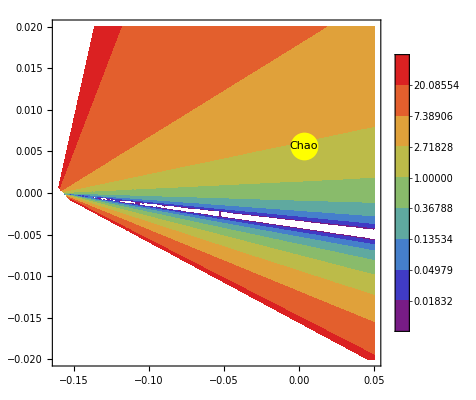

```mathematica
(*(¿O)_1((.b3S)_1)? (¿O)_8((.b3S)_1)= 1.16?, Subscript[O, 8]((.b3S)_1) = x, Subscript[O, 8]((.b9S)_0) = 0.089, Subscript[O, 8]((.b3P)_0) = y*)
J1 =ContourPlot[Subscript[χ1B, η/ψ][1.16,x,0.089,y],{x,-0.2,0.05},{y,-0.02,0.02},RegionFunction->Function[{x,y},B1η[1.16,x,0.089,y]≥0 && B1ψ[1.16,x,0.089,y]>0],ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,25},PlotLegends->Automatic,ScalingFunctions->"Log",Epilog->{PointSize[0.05],Yellow,Point[#]&/@pts1,Black,Text["Chao",#]&/@pts1}]
```

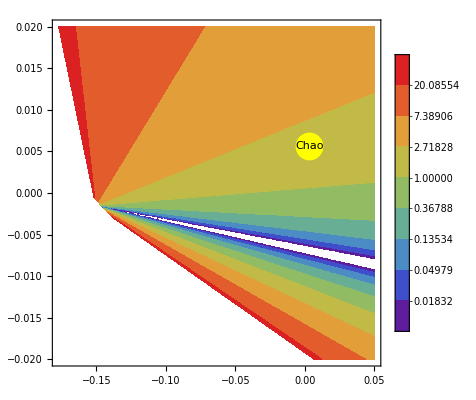

```mathematica
J2 =ContourPlot[Subscript[χ2B, η/ψ][1.16,x,0.089,y],{x,-0.2,0.05},{y,-0.02,0.02},RegionFunction->Function[{x,y},B2η[1.16,x,0.089,y]≥0 && B2ψ[1.16,x,0.089,y]>0],ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,25},PlotLegends->Automatic,ScalingFunctions->"Log",Epilog->{PointSize[0.05],Yellow,Point[#]&/@pts1,Black,Text["Chao",#]&/@pts1}]
```

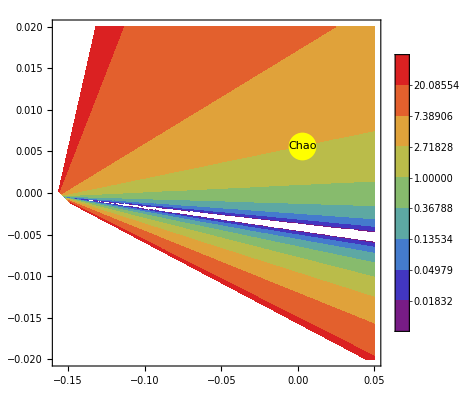

```mathematica
J3 =ContourPlot[Subscript[χ3B, η/ψ][1.16,x,0.089,y],{x,-0.2,0.05},{y,-0.02,0.02},RegionFunction->Function[{x,y},B3η[1.16,x,0.089,y]≥0 && B3ψ[1.16,x,0.089,y]>0],ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,25},PlotLegends->Automatic,ScalingFunctions->"Log",Epilog->{PointSize[0.05],Yellow,Point[#]&/@pts1,Black,Text["Chao",#]&/@pts1}]
```

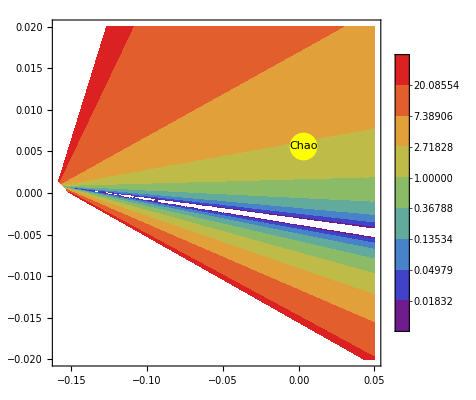

```mathematica
J4 =ContourPlot[Subscript[χ4B, η/ψ][1.16,x,0.089,y],{x,-0.2,0.05},{y,-0.02,0.02},RegionFunction->Function[{x,y},B4η[1.16,x,0.089,y]≥0 && B4ψ[1.16,x,0.089,y]>0],ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,25},PlotLegends->Automatic,ScalingFunctions->"Log",Epilog->{PointSize[0.05],Yellow,Point[#]&/@pts1,Black,Text["Chao",#]&/@pts1}]
```

#### Gráfica 2 J/ψ

```mathematica
(*(¿O)_1((.b3S)_1)? (¿O)_8((.b3S)_1)= 1.16?, Subscript[O, 8]((.b3S)_1) = y, Subscript[O, 8]((.b9S)_0) = x, Subscript[O, 8]((.b3P)_0) = 0.0056*)
```

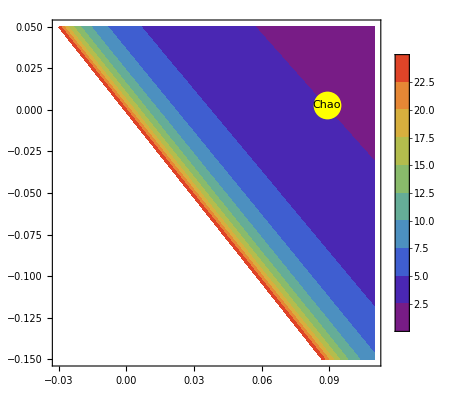

```mathematica
J21=ContourPlot[Subscript[χ1B, η/ψ][1.16,y,x,0.0056],{x,-0.03,0.11},{y,-0.15,0.05},RegionFunction->Function[{x,y},B1η[1.16,y,x,0.0056]≥0 && B1ψ[1.16,y,x,0.0056]>0],ContourStyle->None,ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->{0,25},Epilog->{PointSize[0.05],Yellow,Point[#]&/@pts2,Black,Text["Chao",#]&/@pts2}]
```

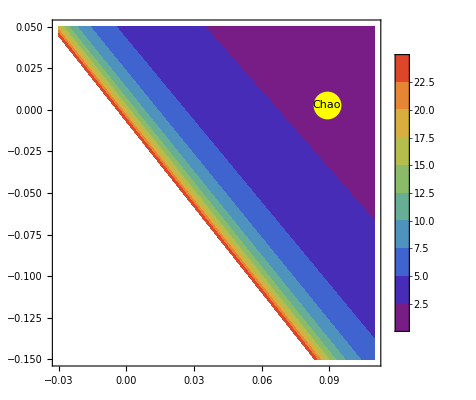

```mathematica
J22=ContourPlot[Subscript[χ2B, η/ψ][1.16,y,x,0.0056],{x,-0.03,0.11},{y,-0.15,0.05},RegionFunction->Function[{x,y},B2η[1.16,y,x,0.0056]≥0 && B2ψ[1.16,y,x,0.0056]>0],ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,25},PlotLegends->Automatic,Epilog->{PointSize[0.05],Yellow,Point[#]&/@pts2,Black,Text["Chao",#]&/@pts2}]
```

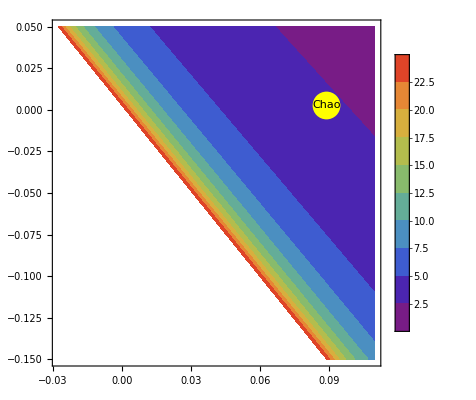

```mathematica
J23=ContourPlot[Subscript[χ3B, η/ψ][1.16,y,x,0.0056],{x,-0.03,0.11},{y,-0.15,0.05},RegionFunction->Function[{x,y},B3η[1.16,y,x,0.0056]≥0 && B3ψ[1.16,y,x,0.0056]>0],ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,25},PlotLegends->Automatic,Epilog->{PointSize[0.05],Yellow,Point[#]&/@pts2,Black,Text["Chao",#]&/@pts2}]
```

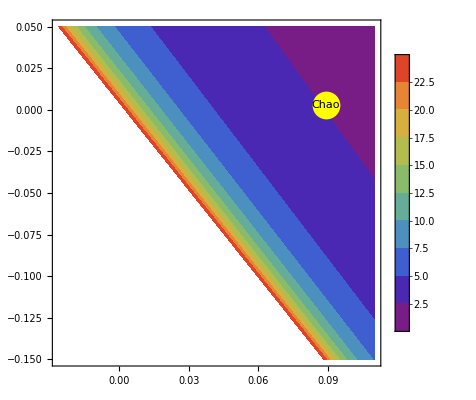

```mathematica
J24=ContourPlot[Subscript[χ4B, η/ψ][1.16,y,x,0.0056],{x,-0.03,0.11},{y,-0.15,0.05},RegionFunction->Function[{x,y},B4η[1.16,y,x,0.0056]≥0 && B4ψ[1.16,y,x,0.0056]>0],ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,25},PlotLegends->Automatic,Epilog->{PointSize[0.05],Yellow,Point[#]&/@pts2,Black,Text["Chao",#]&/@pts2}]
```

```mathematica
GraphicsGrid[{{J21, J22},{J23, J24}}, ImageSize->Large]
```

-Graphics-

#### Gráfica 3 J/ψ

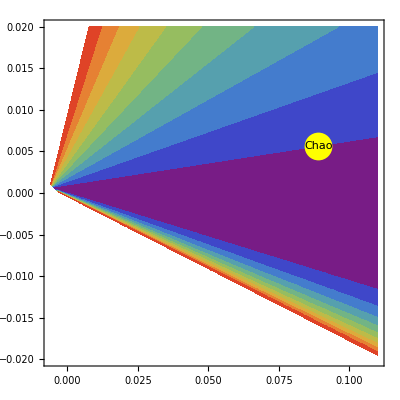

```mathematica
(*(¿O)_1((.b3S)_1)? (¿O)_8((.b3S)_1)= 1.16?, Subscript[O, 8]((.b3S)_1) = 0.003, Subscript[O, 8]((.b9S)_0) = x, Subscript[O, 8]((.b3P)_0) = y*)
J31 =ContourPlot[Subscript[χ1B, η/ψ][1.16,0.003,x,y],{x,-0.03,0.11},{y,-0.02,0.02},RegionFunction->Function[{x,y},B1η[1.16,0.003,x,y]≥0 && B1ψ[1.16,0.003,x,y]>0],ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,25},Epilog->{PointSize[0.05],Yellow,Point[#]&/@pts3,Black,Text["Chao",#]&/@pts3}]
```

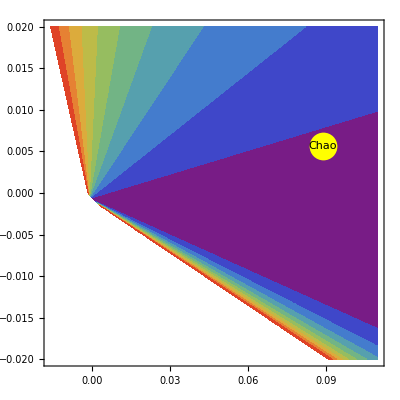

```mathematica
J32 =ContourPlot[Subscript[χ2B, η/ψ][1.16,0.003,x,y],{x,-0.03,0.11},{y,-0.02,0.02},RegionFunction->Function[{x,y},B2η[1.16,0.003,x,y]≥0 && B2ψ[1.16,0.003,x,y]>0],ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,25},Epilog->{PointSize[0.05],Yellow,Point[#]&/@pts3,Black,Text["Chao",#]&/@pts3}]
```

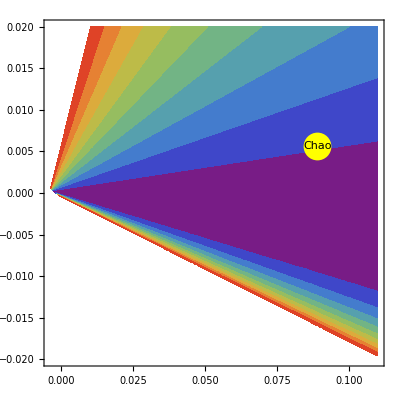

```mathematica
J33 =ContourPlot[Subscript[χ3B, η/ψ][1.16,0.003,x,y],{x,-0.03,0.11},{y,-0.02,0.02},RegionFunction->Function[{x,y},B3η[1.16,0.003,x,y]≥0 && B3ψ[1.16,0.003,x,y]>0],ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,25},Epilog->{PointSize[0.05],Yellow,Point[#]&/@pts3,Black,Text["Chao",#]&/@pts3}]
```

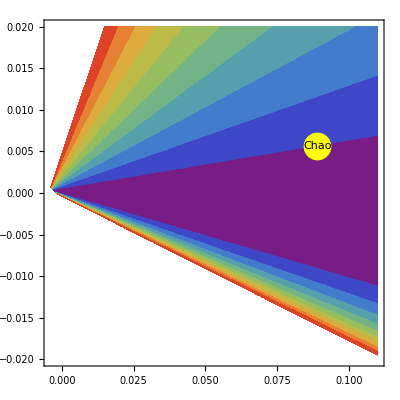

```mathematica
J34 =ContourPlot[Subscript[χ4B, η/ψ][1.16,0.003,x,y],{x,-0.03,0.11},{y,-0.02,0.02},RegionFunction->Function[{x,y},B4η[1.16,0.003,x,y]≥0 && B4ψ[1.16,0.003,x,y]>0],ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,25},Epilog->{PointSize[0.05],Yellow,Point[#]&/@pts3,Black,Text["Chao",#]&/@pts3}]
```

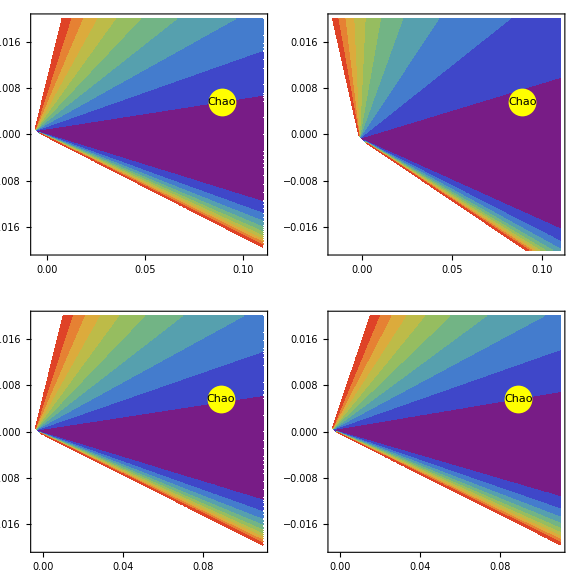

```mathematica
GraphicsGrid[{{J31, J32}, {J33, J34}}, ImageSize->Large]
```

#### Gráfica χc0

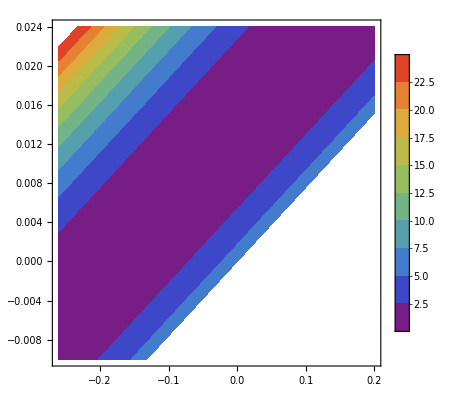

```mathematica
x01 =ContourPlot[Subscript[χ2B1, χc0][x,y],{x,-0.26,0.2},{y,-0.01,0.024},ContourStyle->None,ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->{0,25},RegionFunction->Function[{x,y},Subscript[B1, χc0][x,y]≥0 ]]
```

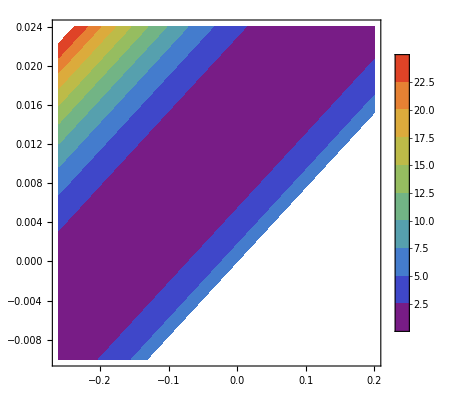

```mathematica
x02 =ContourPlot[Subscript[χ2B2, χc0][x,y],{x,-0.26,0.2},{y,-0.01,0.024},ContourStyle->None,ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->{0,25},RegionFunction->Function[{x,y},Subscript[B2, χc0][x,y]≥0 ]]
```

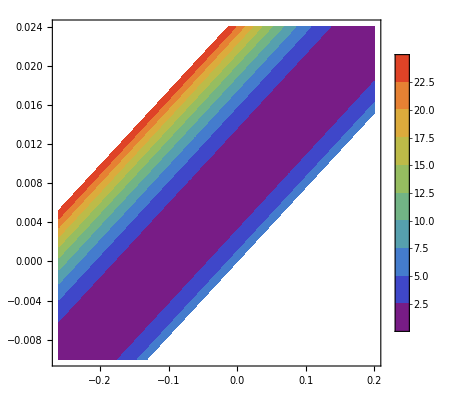

```mathematica
x03 =ContourPlot[Subscript[χ2B3, χc0][x,y],{x,-0.26,0.2},{y,-0.01,0.024},ContourStyle->None,ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->{0,25},RegionFunction->Function[{x,y},Subscript[B3, χc0][x,y]≥0 ]]
```

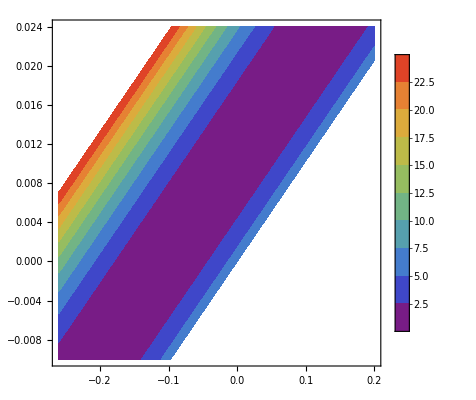

```mathematica
x04 =ContourPlot[Subscript[χ2B4, χc0][x,y],{x,-0.26,0.2},{y,-0.01,0.024},ContourStyle->None,ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->{0,25},RegionFunction->Function[{x,y},Subscript[B4, χc0][x,y]≥0 ]]
```

#### Gráfica χc1

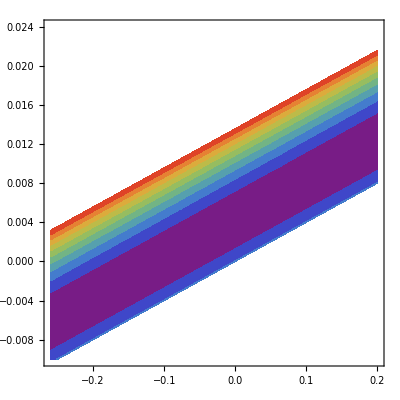

```mathematica
x11 =ContourPlot[Subscript[χ2B1, χc1][x,y],{x,-0.26,0.2},{y,-0.01,0.024},ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,25},RegionFunction->Function[{x,y},Subscript[B1, χc1][x,y]≥0 ]]
```

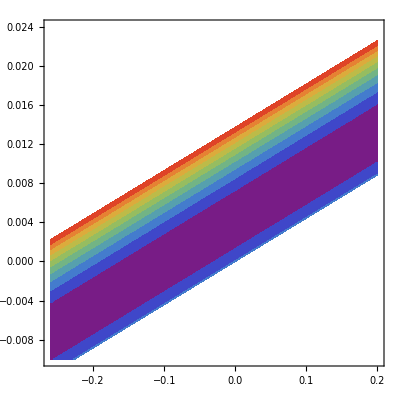

```mathematica
x12 =ContourPlot[Subscript[χ2B2, χc1][x,y],{x,-0.26,0.2},{y,-0.01,0.024},ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,25},RegionFunction->Function[{x,y},Subscript[B2, χc1][x,y]≥0 ]]
```

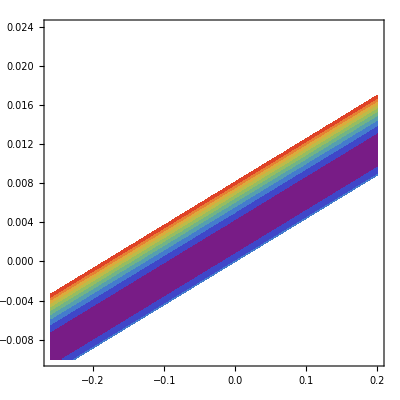

```mathematica
x13 =ContourPlot[Subscript[χ2B3, χc1][x,y],{x,-0.26,0.2},{y,-0.01,0.024},ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,25},RegionFunction->Function[{x,y},Subscript[B3, χc1][x,y]≥0 ]]
```

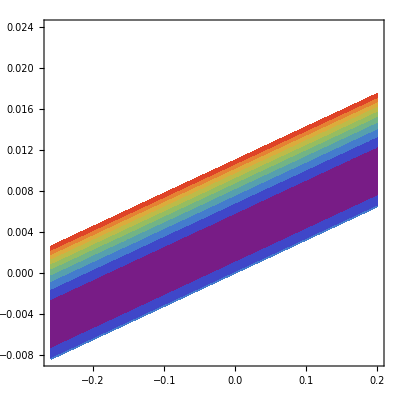

```mathematica
x14 =ContourPlot[Subscript[χ2B4, χc1][x,y],{x,-0.26,0.2},{y,-0.01,0.024},ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,25},RegionFunction->Function[{x,y},Subscript[B4, χc1][x,y]≥0 ]]
```

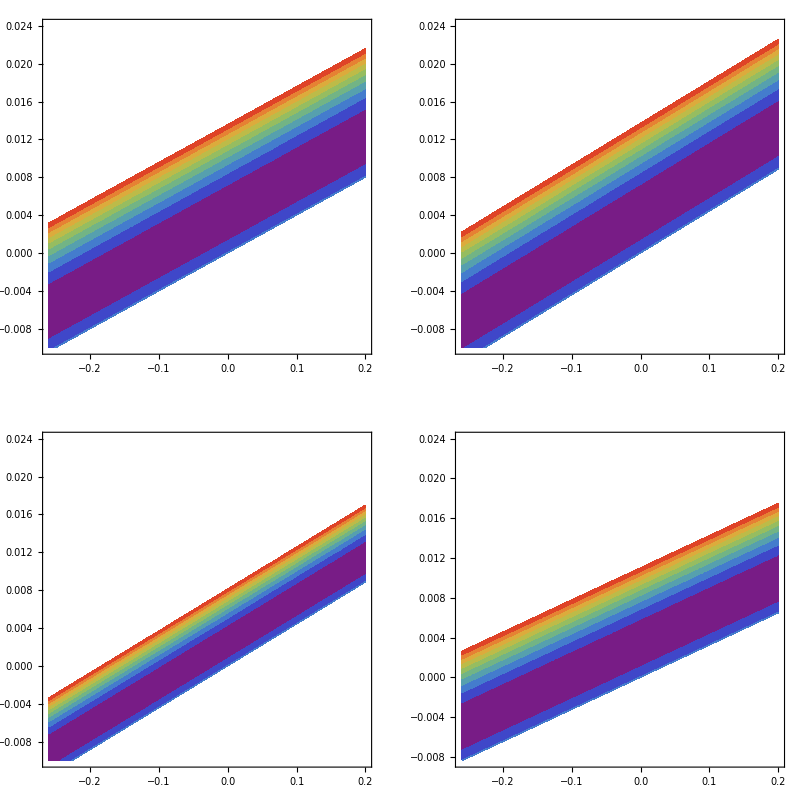

```mathematica
GraphicsGrid[{{x11, x12},{x13, x14}}]
```

#### Gráfica χc2

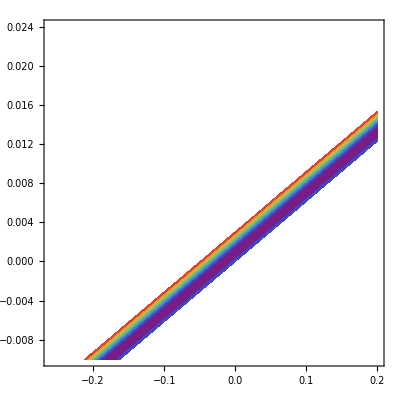

```mathematica
x21 =ContourPlot[Subscript[χ2B1, χc2][x,y],{x,-0.26,0.2},{y,-0.01,0.024},ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,25},RegionFunction->Function[{x,y},Subscript[B1, χc2][x,y]≥0 ]]
```

```mathematica
x22 =ContourPlot[Subscript[χ2B2, χc2][x,y],{x,-0.26,0.2},{y,-0.01,0.024},ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,25},RegionFunction->Function[{x,y},Subscript[B2, χc2][x,y]≥0 ]]
```

-Graphics-

```mathematica
x23 =ContourPlot[Subscript[χ2B3, χc2][x,y],{x,-0.26,0.2},{y,-0.01,0.024},ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,25},RegionFunction->Function[{x,y},Subscript[B3, χc2][x,y]≥0 ]]
```

-Graphics-

```mathematica
x24 =ContourPlot[Subscript[χ2B4, χc2][x,y],{x,-0.26,0.2},{y,-0.01,0.024},ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,25},RegionFunction->Function[{x,y},Subscript[B4, χc2][x,y]≥0 ]]
```

-Graphics-

```mathematica
GraphicsGrid[{{x21, x22},{x23, x24}}, ImageSize->Large]
```

-Graphics-

#### Gráfica χc

```mathematica
xc1 =ContourPlot[Subscript[χ2B1, χc][x,y],{x,-0.26,0.2},{y,-0.01,0.024},ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,25},RegionFunction->Function[{x,y},Subscript[B1, χc0][x,y]≥0 &&Subscript[B1, χc1][x,y]≥0 &&Subscript[B1, χc2][x,y]≥0 ]]
```

-Graphics-

```mathematica
xc2 =ContourPlot[Subscript[χ2B2, χc][x,y],{x,-0.26,0.2},{y,-0.01,0.024},ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,25},RegionFunction->Function[{x,y},Subscript[B2, χc0][x,y]≥0 &&Subscript[B2, χc1][x,y]≥0 &&Subscript[B2, χc2][x,y]≥0 ]]
```

-Graphics-

```mathematica
xc3 =ContourPlot[Subscript[χ2B3, χc][x,y],{x,-0.26,0.2},{y,-0.01,0.024},ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,25},RegionFunction->Function[{x,y},Subscript[B3, χc0][x,y]≥0 &&Subscript[B3, χc1][x,y]≥0 &&Subscript[B3, χc2][x,y]≥0 ]]
```

-Graphics-

```mathematica
xc4 =ContourPlot[Subscript[χ2B4, χc][x,y],{x,-0.26,0.2},{y,-0.01,0.024},ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,25},RegionFunction->Function[{x,y},Subscript[B4, χc0][x,y]≥0 &&Subscript[B4, χc1][x,y]≥0 &&Subscript[B4, χc2][x,y]≥0 ]]
```

-Graphics-

```mathematica
GraphicsGrid[{{xc1, xc2},{xc3, xc4}}]
```

-Graphics-

#### Gráfica χc1/χc0

```mathematica
x101 =ContourPlot[Subscript[χ2B1, χc1/χc0][x,y],{x,-0.08,0.1},{y,-0.003,0.01},ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,25},ScalingFunctions->"Log",RegionFunction->Function[{x,y},Subscript[B1, χc0][x,y]≥0 &&Subscript[B1, χc1][x,y]≥0 ]]
```

-Graphics-

```mathematica
x102 =ContourPlot[Subscript[χ2B2, χc1/χc0][x,y],{x,-0.08,0.1},{y,-0.003,0.01},ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,25},ScalingFunctions->"Log",RegionFunction->Function[{x,y},Subscript[B2, χc0][x,y]≥0 &&Subscript[B2, χc1][x,y]≥0 ]]
```

-Graphics-

```mathematica
x103 =ContourPlot[Subscript[χ2B3, χc1/χc0][x,y],{x,-0.08,0.1},{y,-0.003,0.01},ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,25},ScalingFunctions->"Log",RegionFunction->Function[{x,y},Subscript[B3, χc0][x,y]≥0 &&Subscript[B3, χc1][x,y]≥0 ]]
```

-Graphics-

```mathematica
x104 =ContourPlot[Subscript[χ2B4, χc1/χc0][x,y],{x,-0.08,0.1},{y,-0.003,0.01},ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,25},ScalingFunctions->"Log",RegionFunction->Function[{x,y},Subscript[B4, χc0][x,y]≥0 &&Subscript[B4, χc1][x,y]≥0 ]]
```

-Graphics-

```mathematica
GraphicsGrid[{{x101, x102},{x103, x104}}]
```

-Graphics-

#### Gráfica χc2/χc0

```mathematica
x201 =ContourPlot[Subscript[χ2B1, χc2/χc0][x,y],{x,-0.08,0.1},{y,-0.003,0.01},ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,1600},ScalingFunctions->"Log",RegionFunction->Function[{x,y},Subscript[B1, χc0][x,y]≥0 &&Subscript[B1, χc2][x,y]≥0 ]]
```

-Graphics-

```mathematica
x202 =ContourPlot[Subscript[χ2B1, χc2/χc0][x,y],{x,-0.08,0.1},{y,-0.003,0.01},ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,1600},ScalingFunctions->"Log",RegionFunction->Function[{x,y},Subscript[B2, χc0][x,y]≥0 &&Subscript[B2, χc2][x,y]≥0 ]]
```

-Graphics-

```mathematica
x203 =ContourPlot[Subscript[χ2B3, χc2/χc0][x,y],{x,-0.08,0.1},{y,-0.003,0.01},ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,1600},ScalingFunctions->"Log",RegionFunction->Function[{x,y},Subscript[B3, χc0][x,y]≥0 &&Subscript[B3, χc2][x,y]≥0 ]]
```

-Graphics-

```mathematica
x204 =ContourPlot[Subscript[χ2B4, χc2/χc0][x,y],{x,-0.08,0.1},{y,-0.003,0.01},ContourStyle->None,ColorFunction->"Rainbow",PlotRange->{0,1600},ScalingFunctions->"Log",RegionFunction->Function[{x,y},Subscript[B4, χc0][x,y]≥0 &&Subscript[B4, χc2][x,y]≥0 ]]
```

-Graphics-

```mathematica
GraphicsGrid[{{x201, x202},{x203, x204}}]
```

-Graphics-

#### Gráfica χc/χc0

```mathematica
xc01 =ContourPlot[Subscript[χ2B1, χc/χc0][x,y],{x,-0.08,0.1},{y,-0.003,0.01},ContourStyle->None,ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->{0,1600},ScalingFunctions->"Log",RegionFunction->Function[{x,y},Subscript[B1, χc0][x,y]≥0 &&Subscript[B1, χc1][x,y]≥0 &&Subscript[B1, χc2][x,y]≥0 ]]
```

-Graphics-

```mathematica
xc02 =ContourPlot[Subscript[χ2B2, χc/χc0][x,y],{x,-0.08,0.1},{y,-0.003,0.01},ContourStyle->None,ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->{0,1600},ScalingFunctions->"Log",RegionFunction->Function[{x,y},Subscript[B2, χc0][x,y]≥0 &&Subscript[B2, χc1][x,y]≥0 &&Subscript[B2, χc2][x,y]≥0 ]]
```

-Graphics-

```mathematica
xc03 =ContourPlot[Subscript[χ2B3, χc/χc0][x,y],{x,-0.08,0.1},{y,-0.003,0.01},ContourStyle->None,ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->{0,1600},ScalingFunctions->"Log",RegionFunction->Function[{x,y},Subscript[B3, χc0][x,y]≥0 &&Subscript[B3, χc1][x,y]≥0 &&Subscript[B3, χc2][x,y]≥0 ]]
```

-Graphics-

```mathematica
xc04 =ContourPlot[Subscript[χ2B4, χc/χc0][x,y],{x,-0.08,0.1},{y,-0.003,0.01},ContourStyle->None,ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->{0,1600},ScalingFunctions->"Log",RegionFunction->Function[{x,y},Subscript[B4, χc0][x,y]≥0 &&Subscript[B4, χc1][x,y]≥0 &&Subscript[B4, χc2][x,y]≥0 ]]
```

-Graphics-

#### Mínimos de las funciones χc

```mathematica
(*Los minimos es donde las mediciones van a dar mejor*)
(*Minimo de χc0*)
FindMinimum[{Subscript[χ2B, χc0][x,y],Subscript[B, χc0][x,y]≥0 ,-0.26≤x≤0.2, -0.01≤y≤0.24 },{x,y}]
```

FindMinimum::nrlnum: The function value {B_χc0[1.,1.]} is not a list of real numbers with dimensions {1} at {x,y} = {1.,1.}.

FindMinimum[{χ2B_χc0[x,y],B_χc0[x,y]≥0,-0.26≤x≤0.2,-0.01≤y≤0.24},{x,y}]

```mathematica
(*Minimo de χc1*)
```

```mathematica
FindMinimum[{Subscript[χ2B, χc1][x,y],Subscript[B, χc1][x,y]≥0 ,-0.26≤x≤0.2, -0.01≤y≤0.24 },{x,y}]
```

FindMinimum::nrlnum: The function value {B_χc1[1.,1.]} is not a list of real numbers with dimensions {1} at {x,y} = {1.,1.}.

FindMinimum[{χ2B_χc1[x,y],B_χc1[x,y]≥0,-0.26≤x≤0.2,-0.01≤y≤0.24},{x,y}]

```mathematica
(*Minimo de χc2*)
```

```mathematica
FindMinimum[{Subscript[χ2B, χc2][x,y],Subscript[B, χc2][x,y]≥0 ,-0.26≤x≤0.2, -0.01≤y≤0.24 },{x,y}]
```

FindMinimum::nrlnum: The function value {B_χc2[1.,1.]} is not a list of real numbers with dimensions {1} at {x,y} = {1.,1.}.

FindMinimum[{χ2B_χc2[x,y],B_χc2[x,y]≥0,-0.26≤x≤0.2,-0.01≤y≤0.24},{x,y}]

```mathematica
(*Minimo de χc*)
```

```mathematica
FindMinimum[{Subscript[χ2B, χc][x,y],Subscript[B, χc0][x,y]≥0 &&Subscript[B, χc1][x,y]≥0 &&Subscript[B, χc2][x,y]≥0 ,-0.26≤x≤0.2, -0.01≤y≤0.24 },{x,y}]
```

FindMinimum::nrlnum: The function value {B_χc0[1.,1.],B_χc1[1.,1.],B_χc2[1.,1.]} is not a list of real numbers with dimensions {3} at {x,y} = {1.,1.}.

FindMinimum[{χ2B_χc[x,y],B_χc0[x,y]≥0&&B_χc1[x,y]≥0&&B_χc2[x,y]≥0,-0.26≤x≤0.2,-0.01≤y≤0.24},{x,y}]

```mathematica
(*Minimo de χc1/χc0*)
```

```mathematica
FindMinimum[{Subscript[χ2B, χc1/χc0][x,y],Subscript[B, χc0][x,y]≥0 &&Subscript[B, χc1][x,y]≥0 ,-0.08≤x≤0.1,  0.003≤y≤0.01},{x,y}]
```

FindMinimum::nrlnum: The function value {B_χc0[1.,1.],B_χc1[1.,1.]} is not a list of real numbers with dimensions {2} at {x,y} = {1.,1.}.

FindMinimum[{χ2B_(χc1/χc0)[x,y],B_χc0[x,y]≥0&&B_χc1[x,y]≥0,-0.08≤x≤0.1,0.003≤y≤0.01},{x,y}]

```mathematica
(*Minimo de χc2/χc0*)
```

```mathematica
FindMinimum[{Subscript[χ2B, χc2/χc0][x,y],Subscript[B, χc0][x,y]≥0 &&Subscript[B, χc2][x,y]≥0 ,-0.08≤x≤0.1,  0.003≤y≤0.01 },{x,y}]
```

FindMinimum::nrlnum: The function value {B_χc0[1.,1.],B_χc2[1.,1.]} is not a list of real numbers with dimensions {2} at {x,y} = {1.,1.}.

FindMinimum[{χ2B_(χc2/χc0)[x,y],B_χc0[x,y]≥0&&B_χc2[x,y]≥0,-0.08≤x≤0.1,0.003≤y≤0.01},{x,y}]

```mathematica
(*Minimo de χc/χc0*)
```

```mathematica
FindMinimum[{Subscript[χ2B, χc/χc0][x,y],Subscript[B, χc0][x,y]≥0 &&Subscript[B, χc1][x,y]≥0 &&Subscript[B, χc2][x,y]≥0,-0.08≤x≤0.1, 0.003≤y≤0.01},{x,y}]
```

FindMinimum::nrlnum: The function value {B_χc0[1.,1.],B_χc1[1.,1.],B_χc2[1.,1.]} is not a list of real numbers with dimensions {3} at {x,y} = {1.,1.}.

FindMinimum[{χ2B_(χc/χc0)[x,y],B_χc0[x,y]≥0&&B_χc1[x,y]≥0&&B_χc2[x,y]≥0,-0.08≤x≤0.1,0.003≤y≤0.01},{x,y}]